```mathematica
RandomInteger[2, 10]
```

{1,2,2,1,1,1,0,1,0,2}

```mathematica
RandomInteger[{1,2}, 10]
```

{2,2,1,1,1,1,2,2,1,1}

```mathematica
PalindromeQ[{2,2,1,1,1,1,2,2,1,1}]
```

False

```mathematica
Hold[
PalindromeQ[{2,2,1,1,1,1,2,2,1,1}]]
```

Hold[PalindromeQ[{2,2,1,1,1,1,2,2,1,1}]]

```mathematica
ReleaseHold[Hold[PalindromeQ[{2,2,1,1,1,1,2,2,1,1}]]]
```

False

```mathematica
√π
```

√π

```mathematica
N[√π]
```

1.77245

```mathematica
Log[π]
```

Log[π]

```mathematica
N[Log[π]]
```

1.14473

```mathematica
n^(p-1)==Mod[1, p]
```

n^(-1+p)==Mod[1,p]

```mathematica
FindInstance[n^(-1+p)==Mod[1,p],{n,p}]
```

{{n→Root[{-1+#1^(-79/10-(83 ⅈ)/5)&,-7.72902316404431384963190911046255046257+39.83893045115395341568301342637561481827 ⅈ}],p→-69/10-(83 ⅈ)/5}}

```mathematica
FindInstance[n^(-1+p)==Mod[1,p],{n,p},Reals]
```

{{n→1,p→59/5}}

```mathematica
FindInstance[n^(-1+p)==Mod[1,p],{n,p},Integers]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[n^(-1+p)==Mod[1,p],{n,p},ℤ]

```mathematica
n^p==Mod[n,p]
```

n^p==Mod[n,p]

```mathematica
FindInstance[n^p==Mod[n,p],{n,p}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[n^p==Mod[n,p],{n,p}]

```mathematica
n^p==Mod[n,p]/.{n->56}
```

56^p==Mod[56,p]

```mathematica
n^p==Mod[n,p]/.{n->1}
```

1==Mod[1,p]

```mathematica
1==Mod[1,p]/.p->3
```

True

```mathematica
Mod[1,3]
```

1

```mathematica
Mod[1,4]
```

1

```mathematica
Mod[4,4]
```

0

```mathematica
FullSimplify[
Mod[a,a], Element[a,Integers]]
```

0

```mathematica
FullSimplify[
n^p, And[Element[n,Integers],n>0,Element[p,Primes],Divisible[n,p]]]
```

```mathematica
Divisible[4,2]
```

True

```mathematica
Divisible[2,4]
```

False

```mathematica
FullSimplify[
n^p, And[Element[n,Integers],n>0,Element[p,Primes],Divisible[n,p]]]
```

n^p

```mathematica
GeneratingFunction[n^p,n,x]
```

HurwitzLerchPhi[x,-p,0]

```mathematica
Manipulate[Plot[HurwitzLerchPhi[x,-p,0],{x,-8,8}],{p,-8,8}]
```

```mathematica
10^3
```

1000

```mathematica
1==Mod[1, p]
```

1==Mod[1,p]

```mathematica
Reduce[1==Mod[1,p]]
```

Mod[1,p]==1

```mathematica
FullSimplify[
Mod[1,p], And[Element[p, Integers],p>0]]
```

Mod[1,p]

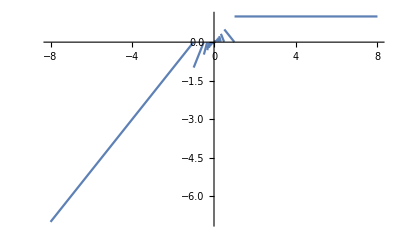

```mathematica
Plot[Mod[1,p],{p,-8,8}]
```

```mathematica
Element[p,Primes]
```

p∈Primes

```mathematica
Mod[1,10]
```

1

```mathematica
n^p==Mod[n,p]
```

n^p==Mod[n,p]

```mathematica
n^p==Mod[n,p]/.n->2
```

2^p==Mod[2,p]

```mathematica
2^p==Mod[2,p]/.p->2
```

False

```mathematica
FunctionExpand[Mod[a,b]]
```

a-b Floor[a/b]

```mathematica
Plot3D[a-b Floor[a/b],{a,-8,8},{b,-8,8}]
```

-Graphics3D-

```mathematica
FunctionExpand[Mod[n,p]]
```

n-p Floor[n/p]

```mathematica
n^p==n-p Floor[n/p]
```

n^p==n-p Floor[n/p]

```mathematica
FullSimplify[
n^p==n-p Floor[n/p], And[Element[n,Integers],n>0,Element[p, Primes]]]
```

n^p+p Floor[n/p]==n

```mathematica
FindInstance[n^p+p Floor[n/p]==n,{n,p}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[n^p+p Floor[n/p]==n,{n,p}]

```mathematica
Table[i->Element[i,Primes],{i,1,100}]
```

{1→False,2→True,3→True,4→False,5→True,6→False,7→True,8→False,9→False,10→False,11→True,12→False,13→True,14→False,15→False,16→False,17→True,18→False,19→True,20→False,21→False,22→False,23→True,24→False,25→False,26→False,27→False,28→False,29→True,30→False,31→True,32→False,33→False,34→False,35→False,36→False,37→True,38→False,39→False,40→False,41→True,42→False,43→True,44→False,45→False,46→False,47→True,48→False,49→False,50→False,51→False,52→False,53→True,54→False,55→False,56→False,57→False,58→False,59→True,60→False,61→True,62→False,63→False,64→False,65→False,66→False,67→True,68→False,69→False,70→False,71→True,72→False,73→True,74→False,75→False,76→False,77→False,78→False,79→True,80→False,81→False,82→False,83→True,84→False,85→False,86→False,87→False,88→False,89→True,90→False,91→False,92→False,93→False,94→False,95→False,96→False,97→True,98→False,99→False,100→False}

```mathematica
FullSimplify[
n^p+p Floor[n/p]==n, p>n]
```

n^p+p Floor[n/p]==n

```mathematica
n^p==n
```

n^p==n

```mathematica
Reduce[n^p==n]
```

(n==0&&Re[p]>0)||(C[1]∈ℤ&&n≠0&&(n==1||(Log[n]≠0&&p==(2 ⅈ π C[1]+Log[n])/Log[n])))

```mathematica
FullSimplify[
n^p==n, And[Element[n,Integers],n>0,p>n,Element[p,Primes]]]
```

n^p==n

```mathematica
FindInstance[n^p==n,{n,p}]
```

{{n→0,p→27+(3 ⅈ)/5}}

```mathematica
FindInstance[n^p==n, {n,p},Integers]
```

{{n→1,p→-24}}

```mathematica
FindInstance[n^p==n, {n,p},Integers,2]
```

{{n→-1,p→315},{n→1,p→124}}

```mathematica
FindInstance[n^p==n, {n,p},Integers,10]
```

{{n→-1,p→1791},{n→199,p→1},{n→-1,p→741},{n→756,p→1},{n→1,p→451},{n→424,p→1},{n→-555,p→1},{n→-1,p→625},{n→-1,p→1063},{n→0,p→118}}

```mathematica
RandomInteger[{0,1}, 10]
```

{1,0,1,0,1,1,1,1,1,0}

```mathematica
Table[{1,i}-> PalindromeQ[Out[53][[;;i]]], {i, 1, 10}]
```

{{1,1}→True,{1,2}→False,{1,3}→True,{1,4}→False,{1,5}→True,{1,6}→False,{1,7}→False,{1,8}→False,{1,9}→False,{1,10}→False}

```mathematica
Table[{1,i}-> Out[53][[;;i]], {i, 1, 10}]
```

{{1,1}→{1},{1,2}→{1,0},{1,3}→{1,0,1},{1,4}→{1,0,1,0},{1,5}→{1,0,1,0,1},{1,6}→{1,0,1,0,1,1},{1,7}→{1,0,1,0,1,1,1},{1,8}→{1,0,1,0,1,1,1,1},{1,9}→{1,0,1,0,1,1,1,1,1},{1,10}→{1,0,1,0,1,1,1,1,1,0}}

```mathematica
Table[{1,i}-> 
{Out[53][[;;i]],
PalindromeQ@Out[53][[;;i]]}, 
{i, 1, Length[Out[53]]}]
```

{{1,1}→{{1},True},{1,2}→{{1,0},False},{1,3}→{{1,0,1},True},{1,4}→{{1,0,1,0},False},{1,5}→{{1,0,1,0,1},True},{1,6}→{{1,0,1,0,1,1},False},{1,7}→{{1,0,1,0,1,1,1},False},{1,8}→{{1,0,1,0,1,1,1,1},False},{1,9}→{{1,0,1,0,1,1,1,1,1},False},{1,10}→{{1,0,1,0,1,1,1,1,1,0},False}}

```mathematica
Table[i-> 
{Out[53][[;;i]],
PalindromeQ@Out[53][[;;i]]}, 
{i, 1, Length[Out[53]]}]
```

{1→{{1},True},2→{{1,0},False},3→{{1,0,1},True},4→{{1,0,1,0},False},5→{{1,0,1,0,1},True},6→{{1,0,1,0,1,1},False},7→{{1,0,1,0,1,1,1},False},8→{{1,0,1,0,1,1,1,1},False},9→{{1,0,1,0,1,1,1,1,1},False},10→{{1,0,1,0,1,1,1,1,1,0},False}}

```mathematica
Print[Table[i-> 
{Out[53][[;;i]],
PalindromeQ@Out[53][[;;i]]}, 
{i, 1, Length[Out[53]]}]]
```

{1→{{1},True},2→{{1,0},False},3→{{1,0,1},True},4→{{1,0,1,0},False},5→{{1,0,1,0,1},True},6→{{1,0,1,0,1,1},False},7→{{1,0,1,0,1,1,1},False},8→{{1,0,1,0,1,1,1,1},False},9→{{1,0,1,0,1,1,1,1,1},False},10→{{1,0,1,0,1,1,1,1,1,0},False}}

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[i-> 
{Out[53][[;;i]],
PalindromeQ@Out[53][[;;i]]}, 
{i, 1, Length[Out[53]]}]]]
```

{1→{{1},True},2→{{1,0},False},3→{{1,0,1},True},4→{{1,0,1,0},False},5→{{1,0,1,0,1},True},6→{{1,0,1,0,1,1},False},7→{{1,0,1,0,1,1,1},False},8→{{1,0,1,0,1,1,1,1},False},9→{{1,0,1,0,1,1,1,1,1},False},10→{{1,0,1,0,1,1,1,1,1,0},False}}

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[i-> 
{Out[53][[;;i]],
PalindromeQ@Out[53][[;;i]]}, 
{i, 1, Length[Out[53]]}]]]
```

{1→{{1},True},2→{{1,0},False},3→{{1,0,1},True},4→{{1,0,1,0},False},5→{{1,0,1,0,1},True},6→{{1,0,1,0,1,1},False},7→{{1,0,1,0,1,1,1},False},8→{{1,0,1,0,1,1,1,1},False},9→{{1,0,1,0,1,1,1,1,1},False},10→{{1,0,1,0,1,1,1,1,1,0},False}}

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[i-> 
{list[[;;i]],
PalindromeQ@list[[;;i]]}, 
{i, 1, Length[list]}]]]
```

{1→{{2},True},2→{{2,1},False},3→{{2,1,1},False},4→{{2,1,1,2},True},5→{{2,1,1,2,2},False},6→{{2,1,1,2,2,1},False},7→{{2,1,1,2,2,1,2},False},8→{{2,1,1,2,2,1,2,2},False},9→{{2,1,1,2,2,1,2,2,2},False},10→{{2,1,1,2,2,1,2,2,2,1},False}}

```mathematica
Table[{i,j},{i,1,3},{j,1,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
Table[{i,j},{i,1,3},{j,1,i}]
```

{{{1,1}},{{2,1},{2,2}},{{3,1},{3,2},{3,3}}}

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[i-> 
{list[[i;;j]],
PalindromeQ[list[[i;;j]]]}, 
{i, 1, Length@list},
{j,1,i}]]]
```

Part::take: Cannot take positions 3 through 1 in {2,1,2,1,2,2,1,1,2,1}.

Part::take: Cannot take positions 4 through 1 in {2,1,2,1,2,2,1,1,2,1}.

General::stop: Further output of Part::take will be suppressed during this calculation.

{{1→{{2},True}},{2→{{},True},2→{{1},True}},{3→{{2,1,2,1,2,2,1,1,2,1}⟦3;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦3;;1⟧]},3→{{},True},3→{{2},True}},{4→{{2,1,2,1,2,2,1,1,2,1}⟦4;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦4;;1⟧]},4→{{2,1,2,1,2,2,1,1,2,1}⟦4;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦4;;2⟧]},4→{{},True},4→{{1},True}},{5→{{2,1,2,1,2,2,1,1,2,1}⟦5;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦5;;1⟧]},5→{{2,1,2,1,2,2,1,1,2,1}⟦5;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦5;;2⟧]},5→{{2,1,2,1,2,2,1,1,2,1}⟦5;;3⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦5;;3⟧]},5→{{},True},5→{{2},True}},{6→{{2,1,2,1,2,2,1,1,2,1}⟦6;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦6;;1⟧]},6→{{2,1,2,1,2,2,1,1,2,1}⟦6;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦6;;2⟧]},6→{{2,1,2,1,2,2,1,1,2,1}⟦6;;3⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦6;;3⟧]},6→{{2,1,2,1,2,2,1,1,2,1}⟦6;;4⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦6;;4⟧]},6→{{},True},6→{{2},True}},{7→{{2,1,2,1,2,2,1,1,2,1}⟦7;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦7;;1⟧]},7→{{2,1,2,1,2,2,1,1,2,1}⟦7;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦7;;2⟧]},7→{{2,1,2,1,2,2,1,1,2,1}⟦7;;3⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦7;;3⟧]},7→{{2,1,2,1,2,2,1,1,2,1}⟦7;;4⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦7;;4⟧]},7→{{2,1,2,1,2,2,1,1,2,1}⟦7;;5⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦7;;5⟧]},7→{{},True},7→{{1},True}},{8→{{2,1,2,1,2,2,1,1,2,1}⟦8;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦8;;1⟧]},8→{{2,1,2,1,2,2,1,1,2,1}⟦8;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦8;;2⟧]},8→{{2,1,2,1,2,2,1,1,2,1}⟦8;;3⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦8;;3⟧]},8→{{2,1,2,1,2,2,1,1,2,1}⟦8;;4⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦8;;4⟧]},8→{{2,1,2,1,2,2,1,1,2,1}⟦8;;5⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦8;;5⟧]},8→{{2,1,2,1,2,2,1,1,2,1}⟦8;;6⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦8;;6⟧]},8→{{},True},8→{{1},True}},{9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;1⟧]},9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;2⟧]},9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;3⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;3⟧]},9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;4⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;4⟧]},9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;5⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;5⟧]},9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;6⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;6⟧]},9→{{2,1,2,1,2,2,1,1,2,1}⟦9;;7⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦9;;7⟧]},9→{{},True},9→{{2},True}},{10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;1⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;1⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;2⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;2⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;3⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;3⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;4⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;4⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;5⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;5⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;6⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;6⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;7⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;7⟧]},10→{{2,1,2,1,2,2,1,1,2,1}⟦10;;8⟧,PalindromeQ[{2,1,2,1,2,2,1,1,2,1}⟦10;;8⟧]},10→{{},True},10→{{1},True}}}

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[{i,j}, (* list[[i;;j]] *) 
{i, 1, Length@list},
{j,1,i}]]]
```

{{{1,1}},{{2,1},{2,2}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3},{4,4}},{{5,1},{5,2},{5,3},{5,4},{5,5}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}}

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[{i,j}->list[[i;;j]],
{i, 1, Length@list},
{j,1,i}]]]
```

Part::take: Cannot take positions 3 through 1 in {2,2,2,2,1,1,1,2,2,1}.

Part::take: Cannot take positions 4 through 1 in {2,2,2,2,1,1,1,2,2,1}.

Part::take: Cannot take positions 4 through 2 in {2,2,2,2,1,1,1,2,2,1}.

General::stop: Further output of Part::take will be suppressed during this calculation.

{{{1,1}→{2}},{{2,1}→{},{2,2}→{2}},{{3,1}→{2,2,2,2,1,1,1,2,2,1}⟦3;;1⟧,{3,2}→{},{3,3}→{2}},{{4,1}→{2,2,2,2,1,1,1,2,2,1}⟦4;;1⟧,{4,2}→{2,2,2,2,1,1,1,2,2,1}⟦4;;2⟧,{4,3}→{},{4,4}→{2}},{{5,1}→{2,2,2,2,1,1,1,2,2,1}⟦5;;1⟧,{5,2}→{2,2,2,2,1,1,1,2,2,1}⟦5;;2⟧,{5,3}→{2,2,2,2,1,1,1,2,2,1}⟦5;;3⟧,{5,4}→{},{5,5}→{1}},{{6,1}→{2,2,2,2,1,1,1,2,2,1}⟦6;;1⟧,{6,2}→{2,2,2,2,1,1,1,2,2,1}⟦6;;2⟧,{6,3}→{2,2,2,2,1,1,1,2,2,1}⟦6;;3⟧,{6,4}→{2,2,2,2,1,1,1,2,2,1}⟦6;;4⟧,{6,5}→{},{6,6}→{1}},{{7,1}→{2,2,2,2,1,1,1,2,2,1}⟦7;;1⟧,{7,2}→{2,2,2,2,1,1,1,2,2,1}⟦7;;2⟧,{7,3}→{2,2,2,2,1,1,1,2,2,1}⟦7;;3⟧,{7,4}→{2,2,2,2,1,1,1,2,2,1}⟦7;;4⟧,{7,5}→{2,2,2,2,1,1,1,2,2,1}⟦7;;5⟧,{7,6}→{},{7,7}→{1}},{{8,1}→{2,2,2,2,1,1,1,2,2,1}⟦8;;1⟧,{8,2}→{2,2,2,2,1,1,1,2,2,1}⟦8;;2⟧,{8,3}→{2,2,2,2,1,1,1,2,2,1}⟦8;;3⟧,{8,4}→{2,2,2,2,1,1,1,2,2,1}⟦8;;4⟧,{8,5}→{2,2,2,2,1,1,1,2,2,1}⟦8;;5⟧,{8,6}→{2,2,2,2,1,1,1,2,2,1}⟦8;;6⟧,{8,7}→{},{8,8}→{2}},{{9,1}→{2,2,2,2,1,1,1,2,2,1}⟦9;;1⟧,{9,2}→{2,2,2,2,1,1,1,2,2,1}⟦9;;2⟧,{9,3}→{2,2,2,2,1,1,1,2,2,1}⟦9;;3⟧,{9,4}→{2,2,2,2,1,1,1,2,2,1}⟦9;;4⟧,{9,5}→{2,2,2,2,1,1,1,2,2,1}⟦9;;5⟧,{9,6}→{2,2,2,2,1,1,1,2,2,1}⟦9;;6⟧,{9,7}→{2,2,2,2,1,1,1,2,2,1}⟦9;;7⟧,{9,8}→{},{9,9}→{2}},{{10,1}→{2,2,2,2,1,1,1,2,2,1}⟦10;;1⟧,{10,2}→{2,2,2,2,1,1,1,2,2,1}⟦10;;2⟧,{10,3}→{2,2,2,2,1,1,1,2,2,1}⟦10;;3⟧,{10,4}→{2,2,2,2,1,1,1,2,2,1}⟦10;;4⟧,{10,5}→{2,2,2,2,1,1,1,2,2,1}⟦10;;5⟧,{10,6}→{2,2,2,2,1,1,1,2,2,1}⟦10;;6⟧,{10,7}→{2,2,2,2,1,1,1,2,2,1}⟦10;;7⟧,{10,8}→{2,2,2,2,1,1,1,2,2,1}⟦10;;8⟧,{10,9}→{},{10,10}→{1}}}

```mathematica
{2,2,2,2,1,1,1,2,2,1}⟦3;;1⟧
```

Part::take: Cannot take positions 3 through 1 in {2,2,2,2,1,1,1,2,2,1}.

{2,2,2,2,1,1,1,2,2,1}⟦3;;1⟧

```mathematica
{2,2,2,2,1,1,1,2,2,1}[[3;;1]]
```

Part::take: Cannot take positions 3 through 1 in {2,2,2,2,1,1,1,2,2,1}.

{2,2,2,2,1,1,1,2,2,1}⟦3;;1⟧

```mathematica
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[{j,i}->
list[[j;;i]]->
PalindromeQ[list[[j;;i]]],
{i, 1, Length@list},
{j,1,i}]]]
```

{{{1,1}→{2}→True},{{1,2}→{2,2}→True,{2,2}→{2}→True},{{1,3}→{2,2,2}→True,{2,3}→{2,2}→True,{3,3}→{2}→True},{{1,4}→{2,2,2,2}→True,{2,4}→{2,2,2}→True,{3,4}→{2,2}→True,{4,4}→{2}→True},{{1,5}→{2,2,2,2,1}→False,{2,5}→{2,2,2,1}→False,{3,5}→{2,2,1}→False,{4,5}→{2,1}→False,{5,5}→{1}→True},{{1,6}→{2,2,2,2,1,2}→False,{2,6}→{2,2,2,1,2}→False,{3,6}→{2,2,1,2}→False,{4,6}→{2,1,2}→True,{5,6}→{1,2}→False,{6,6}→{2}→True},{{1,7}→{2,2,2,2,1,2,2}→False,{2,7}→{2,2,2,1,2,2}→False,{3,7}→{2,2,1,2,2}→True,{4,7}→{2,1,2,2}→False,{5,7}→{1,2,2}→False,{6,7}→{2,2}→True,{7,7}→{2}→True},{{1,8}→{2,2,2,2,1,2,2,1}→False,{2,8}→{2,2,2,1,2,2,1}→False,{3,8}→{2,2,1,2,2,1}→False,{4,8}→{2,1,2,2,1}→False,{5,8}→{1,2,2,1}→True,{6,8}→{2,2,1}→False,{7,8}→{2,1}→False,{8,8}→{1}→True},{{1,9}→{2,2,2,2,1,2,2,1,1}→False,{2,9}→{2,2,2,1,2,2,1,1}→False,{3,9}→{2,2,1,2,2,1,1}→False,{4,9}→{2,1,2,2,1,1}→False,{5,9}→{1,2,2,1,1}→False,{6,9}→{2,2,1,1}→False,{7,9}→{2,1,1}→False,{8,9}→{1,1}→True,{9,9}→{1}→True},{{1,10}→{2,2,2,2,1,2,2,1,1,2}→False,{2,10}→{2,2,2,1,2,2,1,1,2}→False,{3,10}→{2,2,1,2,2,1,1,2}→False,{4,10}→{2,1,2,2,1,1,2}→False,{5,10}→{1,2,2,1,1,2}→False,{6,10}→{2,2,1,1,2}→False,{7,10}→{2,1,1,2}→True,{8,10}→{1,1,2}→False,{9,10}→{1,2}→False,{10,10}→{2}→True}}

```mathematica
Flatten[
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[{j,i}->
list[[j;;i]]->
PalindromeQ[list[[j;;i]]],
{i, 1, Length@list},
{j,1,i}]]],1]
```

{{1,1}→{1}→True,{1,2}→{1,2}→False,{2,2}→{2}→True,{1,3}→{1,2,2}→False,{2,3}→{2,2}→True,{3,3}→{2}→True,{1,4}→{1,2,2,1}→True,{2,4}→{2,2,1}→False,{3,4}→{2,1}→False,{4,4}→{1}→True,{1,5}→{1,2,2,1,1}→False,{2,5}→{2,2,1,1}→False,{3,5}→{2,1,1}→False,{4,5}→{1,1}→True,{5,5}→{1}→True,{1,6}→{1,2,2,1,1,1}→False,{2,6}→{2,2,1,1,1}→False,{3,6}→{2,1,1,1}→False,{4,6}→{1,1,1}→True,{5,6}→{1,1}→True,{6,6}→{1}→True,{1,7}→{1,2,2,1,1,1,2}→False,{2,7}→{2,2,1,1,1,2}→False,{3,7}→{2,1,1,1,2}→True,{4,7}→{1,1,1,2}→False,{5,7}→{1,1,2}→False,{6,7}→{1,2}→False,{7,7}→{2}→True,{1,8}→{1,2,2,1,1,1,2,2}→False,{2,8}→{2,2,1,1,1,2,2}→True,{3,8}→{2,1,1,1,2,2}→False,{4,8}→{1,1,1,2,2}→False,{5,8}→{1,1,2,2}→False,{6,8}→{1,2,2}→False,{7,8}→{2,2}→True,{8,8}→{2}→True,{1,9}→{1,2,2,1,1,1,2,2,2}→False,{2,9}→{2,2,1,1,1,2,2,2}→False,{3,9}→{2,1,1,1,2,2,2}→False,{4,9}→{1,1,1,2,2,2}→False,{5,9}→{1,1,2,2,2}→False,{6,9}→{1,2,2,2}→False,{7,9}→{2,2,2}→True,{8,9}→{2,2}→True,{9,9}→{2}→True,{1,10}→{1,2,2,1,1,1,2,2,2,1}→False,{2,10}→{2,2,1,1,1,2,2,2,1}→False,{3,10}→{2,1,1,1,2,2,2,1}→False,{4,10}→{1,1,1,2,2,2,1}→False,{5,10}→{1,1,2,2,2,1}→False,{6,10}→{1,2,2,2,1}→True,{7,10}→{2,2,2,1}→False,{8,10}→{2,2,1}→False,{9,10}→{2,1}→False,{10,10}→{1}→True}

```mathematica
Flatten[
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}]]],1]
```

{{{1,1},{1},True,1},{{1,2},{1,2},False,2},{{2,2},{2},True,1},{{1,3},{1,2,1},True,3},{{2,3},{2,1},False,2},{{3,3},{1},True,1},{{1,4},{1,2,1,2},False,4},{{2,4},{2,1,2},True,3},{{3,4},{1,2},False,2},{{4,4},{2},True,1},{{1,5},{1,2,1,2,2},False,5},{{2,5},{2,1,2,2},False,4},{{3,5},{1,2,2},False,3},{{4,5},{2,2},True,2},{{5,5},{2},True,1},{{1,6},{1,2,1,2,2,1},False,6},{{2,6},{2,1,2,2,1},False,5},{{3,6},{1,2,2,1},True,4},{{4,6},{2,2,1},False,3},{{5,6},{2,1},False,2},{{6,6},{1},True,1},{{1,7},{1,2,1,2,2,1,2},False,7},{{2,7},{2,1,2,2,1,2},True,6},{{3,7},{1,2,2,1,2},False,5},{{4,7},{2,2,1,2},False,4},{{5,7},{2,1,2},True,3},{{6,7},{1,2},False,2},{{7,7},{2},True,1},{{1,8},{1,2,1,2,2,1,2,2},False,8},{{2,8},{2,1,2,2,1,2,2},False,7},{{3,8},{1,2,2,1,2,2},False,6},{{4,8},{2,2,1,2,2},True,5},{{5,8},{2,1,2,2},False,4},{{6,8},{1,2,2},False,3},{{7,8},{2,2},True,2},{{8,8},{2},True,1},{{1,9},{1,2,1,2,2,1,2,2,1},False,9},{{2,9},{2,1,2,2,1,2,2,1},False,8},{{3,9},{1,2,2,1,2,2,1},True,7},{{4,9},{2,2,1,2,2,1},False,6},{{5,9},{2,1,2,2,1},False,5},{{6,9},{1,2,2,1},True,4},{{7,9},{2,2,1},False,3},{{8,9},{2,1},False,2},{{9,9},{1},True,1},{{1,10},{1,2,1,2,2,1,2,2,1,2},False,10},{{2,10},{2,1,2,2,1,2,2,1,2},True,9},{{3,10},{1,2,2,1,2,2,1,2},False,8},{{4,10},{2,2,1,2,2,1,2},False,7},{{5,10},{2,1,2,2,1,2},True,6},{{6,10},{1,2,2,1,2},False,5},{{7,10},{2,2,1,2},False,4},{{8,10},{2,1,2},True,3},{{9,10},{1,2},False,2},{{10,10},{2},True,1}}

```mathematica
Flatten[
With[{limit=10},
With[{list=RandomInteger[{1,2},limit]},
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}]]],1]
```

```mathematica
RandomInteger[{1,2},20]
```

{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2}

```mathematica
list={2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2}
```

{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2}

```mathematica
limit=Length@list
```

20

```mathematica
Flatten[
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}],1]
```

{{{1,1},{2},True,1},{{1,2},{2,2},True,2},{{2,2},{2},True,1},{{1,3},{2,2,1},False,3},{{2,3},{2,1},False,2},{{3,3},{1},True,1},{{1,4},{2,2,1,2},False,4},{{2,4},{2,1,2},True,3},{{3,4},{1,2},False,2},{{4,4},{2},True,1},{{1,5},{2,2,1,2,2},True,5},{{2,5},{2,1,2,2},False,4},{{3,5},{1,2,2},False,3},{{4,5},{2,2},True,2},{{5,5},{2},True,1},{{1,6},{2,2,1,2,2,2},False,6},{{2,6},{2,1,2,2,2},False,5},{{3,6},{1,2,2,2},False,4},{{4,6},{2,2,2},True,3},{{5,6},{2,2},True,2},{{6,6},{2},True,1},{{1,7},{2,2,1,2,2,2,1},False,7},{{2,7},{2,1,2,2,2,1},False,6},{{3,7},{1,2,2,2,1},True,5},{{4,7},{2,2,2,1},False,4},{{5,7},{2,2,1},False,3},{{6,7},{2,1},False,2},{{7,7},{1},True,1},{{1,8},{2,2,1,2,2,2,1,2},False,8},{{2,8},{2,1,2,2,2,1,2},True,7},{{3,8},{1,2,2,2,1,2},False,6},{{4,8},{2,2,2,1,2},False,5},{{5,8},{2,2,1,2},False,4},{{6,8},{2,1,2},True,3},{{7,8},{1,2},False,2},{{8,8},{2},True,1},{{1,9},{2,2,1,2,2,2,1,2,1},False,9},{{2,9},{2,1,2,2,2,1,2,1},False,8},{{3,9},{1,2,2,2,1,2,1},False,7},{{4,9},{2,2,2,1,2,1},False,6},{{5,9},{2,2,1,2,1},False,5},{{6,9},{2,1,2,1},False,4},{{7,9},{1,2,1},True,3},{{8,9},{2,1},False,2},{{9,9},{1},True,1},{{1,10},{2,2,1,2,2,2,1,2,1,2},False,10},{{2,10},{2,1,2,2,2,1,2,1,2},False,9},{{3,10},{1,2,2,2,1,2,1,2},False,8},{{4,10},{2,2,2,1,2,1,2},False,7},{{5,10},{2,2,1,2,1,2},False,6},{{6,10},{2,1,2,1,2},True,5},{{7,10},{1,2,1,2},False,4},{{8,10},{2,1,2},True,3},{{9,10},{1,2},False,2},{{10,10},{2},True,1},{{1,11},{2,2,1,2,2,2,1,2,1,2,1},False,11},{{2,11},{2,1,2,2,2,1,2,1,2,1},False,10},{{3,11},{1,2,2,2,1,2,1,2,1},False,9},{{4,11},{2,2,2,1,2,1,2,1},False,8},{{5,11},{2,2,1,2,1,2,1},False,7},{{6,11},{2,1,2,1,2,1},False,6},{{7,11},{1,2,1,2,1},True,5},{{8,11},{2,1,2,1},False,4},{{9,11},{1,2,1},True,3},{{10,11},{2,1},False,2},{{11,11},{1},True,1},{{1,12},{2,2,1,2,2,2,1,2,1,2,1,1},False,12},{{2,12},{2,1,2,2,2,1,2,1,2,1,1},False,11},{{3,12},{1,2,2,2,1,2,1,2,1,1},False,10},{{4,12},{2,2,2,1,2,1,2,1,1},False,9},{{5,12},{2,2,1,2,1,2,1,1},False,8},{{6,12},{2,1,2,1,2,1,1},False,7},{{7,12},{1,2,1,2,1,1},False,6},{{8,12},{2,1,2,1,1},False,5},{{9,12},{1,2,1,1},False,4},{{10,12},{2,1,1},False,3},{{11,12},{1,1},True,2},{{12,12},{1},True,1},{{1,13},{2,2,1,2,2,2,1,2,1,2,1,1,2},False,13},{{2,13},{2,1,2,2,2,1,2,1,2,1,1,2},False,12},{{3,13},{1,2,2,2,1,2,1,2,1,1,2},False,11},{{4,13},{2,2,2,1,2,1,2,1,1,2},False,10},{{5,13},{2,2,1,2,1,2,1,1,2},False,9},{{6,13},{2,1,2,1,2,1,1,2},False,8},{{7,13},{1,2,1,2,1,1,2},False,7},{{8,13},{2,1,2,1,1,2},False,6},{{9,13},{1,2,1,1,2},False,5},{{10,13},{2,1,1,2},True,4},{{11,13},{1,1,2},False,3},{{12,13},{1,2},False,2},{{13,13},{2},True,1},{{1,14},{2,2,1,2,2,2,1,2,1,2,1,1,2,2},False,14},{{2,14},{2,1,2,2,2,1,2,1,2,1,1,2,2},False,13},{{3,14},{1,2,2,2,1,2,1,2,1,1,2,2},False,12},{{4,14},{2,2,2,1,2,1,2,1,1,2,2},False,11},{{5,14},{2,2,1,2,1,2,1,1,2,2},False,10},{{6,14},{2,1,2,1,2,1,1,2,2},False,9},{{7,14},{1,2,1,2,1,1,2,2},False,8},{{8,14},{2,1,2,1,1,2,2},False,7},{{9,14},{1,2,1,1,2,2},False,6},{{10,14},{2,1,1,2,2},False,5},{{11,14},{1,1,2,2},False,4},{{12,14},{1,2,2},False,3},{{13,14},{2,2},True,2},{{14,14},{2},True,1},{{1,15},{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1},False,15},{{2,15},{2,1,2,2,2,1,2,1,2,1,1,2,2,1},False,14},{{3,15},{1,2,2,2,1,2,1,2,1,1,2,2,1},False,13},{{4,15},{2,2,2,1,2,1,2,1,1,2,2,1},False,12},{{5,15},{2,2,1,2,1,2,1,1,2,2,1},False,11},{{6,15},{2,1,2,1,2,1,1,2,2,1},False,10},{{7,15},{1,2,1,2,1,1,2,2,1},False,9},{{8,15},{2,1,2,1,1,2,2,1},False,8},{{9,15},{1,2,1,1,2,2,1},False,7},{{10,15},{2,1,1,2,2,1},False,6},{{11,15},{1,1,2,2,1},False,5},{{12,15},{1,2,2,1},True,4},{{13,15},{2,2,1},False,3},{{14,15},{2,1},False,2},{{15,15},{1},True,1},{{1,16},{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1},False,16},{{2,16},{2,1,2,2,2,1,2,1,2,1,1,2,2,1,1},False,15},{{3,16},{1,2,2,2,1,2,1,2,1,1,2,2,1,1},False,14},{{4,16},{2,2,2,1,2,1,2,1,1,2,2,1,1},False,13},{{5,16},{2,2,1,2,1,2,1,1,2,2,1,1},False,12},{{6,16},{2,1,2,1,2,1,1,2,2,1,1},False,11},{{7,16},{1,2,1,2,1,1,2,2,1,1},False,10},{{8,16},{2,1,2,1,1,2,2,1,1},False,9},{{9,16},{1,2,1,1,2,2,1,1},False,8},{{10,16},{2,1,1,2,2,1,1},False,7},{{11,16},{1,1,2,2,1,1},True,6},{{12,16},{1,2,2,1,1},False,5},{{13,16},{2,2,1,1},False,4},{{14,16},{2,1,1},False,3},{{15,16},{1,1},True,2},{{16,16},{1},True,1},{{1,17},{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1},False,17},{{2,17},{2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1},False,16},{{3,17},{1,2,2,2,1,2,1,2,1,1,2,2,1,1,1},False,15},{{4,17},{2,2,2,1,2,1,2,1,1,2,2,1,1,1},False,14},{{5,17},{2,2,1,2,1,2,1,1,2,2,1,1,1},False,13},{{6,17},{2,1,2,1,2,1,1,2,2,1,1,1},False,12},{{7,17},{1,2,1,2,1,1,2,2,1,1,1},False,11},{{8,17},{2,1,2,1,1,2,2,1,1,1},False,10},{{9,17},{1,2,1,1,2,2,1,1,1},False,9},{{10,17},{2,1,1,2,2,1,1,1},False,8},{{11,17},{1,1,2,2,1,1,1},False,7},{{12,17},{1,2,2,1,1,1},False,6},{{13,17},{2,2,1,1,1},False,5},{{14,17},{2,1,1,1},False,4},{{15,17},{1,1,1},True,3},{{16,17},{1,1},True,2},{{17,17},{1},True,1},{{1,18},{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2},False,18},{{2,18},{2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2},False,17},{{3,18},{1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2},False,16},{{4,18},{2,2,2,1,2,1,2,1,1,2,2,1,1,1,2},False,15},{{5,18},{2,2,1,2,1,2,1,1,2,2,1,1,1,2},False,14},{{6,18},{2,1,2,1,2,1,1,2,2,1,1,1,2},False,13},{{7,18},{1,2,1,2,1,1,2,2,1,1,1,2},False,12},{{8,18},{2,1,2,1,1,2,2,1,1,1,2},False,11},{{9,18},{1,2,1,1,2,2,1,1,1,2},False,10},{{10,18},{2,1,1,2,2,1,1,1,2},False,9},{{11,18},{1,1,2,2,1,1,1,2},False,8},{{12,18},{1,2,2,1,1,1,2},False,7},{{13,18},{2,2,1,1,1,2},False,6},{{14,18},{2,1,1,1,2},True,5},{{15,18},{1,1,1,2},False,4},{{16,18},{1,1,2},False,3},{{17,18},{1,2},False,2},{{18,18},{2},True,1},{{1,19},{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2},False,19},{{2,19},{2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2},False,18},{{3,19},{1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2},False,17},{{4,19},{2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2},False,16},{{5,19},{2,2,1,2,1,2,1,1,2,2,1,1,1,2,2},False,15},{{6,19},{2,1,2,1,2,1,1,2,2,1,1,1,2,2},False,14},{{7,19},{1,2,1,2,1,1,2,2,1,1,1,2,2},False,13},{{8,19},{2,1,2,1,1,2,2,1,1,1,2,2},False,12},{{9,19},{1,2,1,1,2,2,1,1,1,2,2},False,11},{{10,19},{2,1,1,2,2,1,1,1,2,2},False,10},{{11,19},{1,1,2,2,1,1,1,2,2},False,9},{{12,19},{1,2,2,1,1,1,2,2},False,8},{{13,19},{2,2,1,1,1,2,2},True,7},{{14,19},{2,1,1,1,2,2},False,6},{{15,19},{1,1,1,2,2},False,5},{{16,19},{1,1,2,2},False,4},{{17,19},{1,2,2},False,3},{{18,19},{2,2},True,2},{{19,19},{2},True,1},{{1,20},{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,20},{{2,20},{2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,19},{{3,20},{1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,18},{{4,20},{2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,17},{{5,20},{2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,16},{{6,20},{2,1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,15},{{7,20},{1,2,1,2,1,1,2,2,1,1,1,2,2,2},False,14},{{8,20},{2,1,2,1,1,2,2,1,1,1,2,2,2},False,13},{{9,20},{1,2,1,1,2,2,1,1,1,2,2,2},False,12},{{10,20},{2,1,1,2,2,1,1,1,2,2,2},False,11},{{11,20},{1,1,2,2,1,1,1,2,2,2},False,10},{{12,20},{1,2,2,1,1,1,2,2,2},False,9},{{13,20},{2,2,1,1,1,2,2,2},False,8},{{14,20},{2,1,1,1,2,2,2},False,7},{{15,20},{1,1,1,2,2,2},False,6},{{16,20},{1,1,2,2,2},False,5},{{17,20},{1,2,2,2},False,4},{{18,20},{2,2,2},True,3},{{19,20},{2,2},True,2},{{20,20},{2},True,1}}

```mathematica
Select[
Flatten[
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}],1],
#[[3]]&]
```

{{{1,1},{2},True,1},{{1,2},{2,2},True,2},{{2,2},{2},True,1},{{3,3},{1},True,1},{{2,4},{2,1,2},True,3},{{4,4},{2},True,1},{{1,5},{2,2,1,2,2},True,5},{{4,5},{2,2},True,2},{{5,5},{2},True,1},{{4,6},{2,2,2},True,3},{{5,6},{2,2},True,2},{{6,6},{2},True,1},{{3,7},{1,2,2,2,1},True,5},{{7,7},{1},True,1},{{2,8},{2,1,2,2,2,1,2},True,7},{{6,8},{2,1,2},True,3},{{8,8},{2},True,1},{{7,9},{1,2,1},True,3},{{9,9},{1},True,1},{{6,10},{2,1,2,1,2},True,5},{{8,10},{2,1,2},True,3},{{10,10},{2},True,1},{{7,11},{1,2,1,2,1},True,5},{{9,11},{1,2,1},True,3},{{11,11},{1},True,1},{{11,12},{1,1},True,2},{{12,12},{1},True,1},{{10,13},{2,1,1,2},True,4},{{13,13},{2},True,1},{{13,14},{2,2},True,2},{{14,14},{2},True,1},{{12,15},{1,2,2,1},True,4},{{15,15},{1},True,1},{{11,16},{1,1,2,2,1,1},True,6},{{15,16},{1,1},True,2},{{16,16},{1},True,1},{{15,17},{1,1,1},True,3},{{16,17},{1,1},True,2},{{17,17},{1},True,1},{{14,18},{2,1,1,1,2},True,5},{{18,18},{2},True,1},{{13,19},{2,2,1,1,1,2,2},True,7},{{18,19},{2,2},True,2},{{19,19},{2},True,1},{{18,20},{2,2,2},True,3},{{19,20},{2,2},True,2},{{20,20},{2},True,1}}

```mathematica
Reverse@SortBy[
Select[
Flatten[
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}],1],
#[[3]]&],Last]
```

{{{13,19},{2,2,1,1,1,2,2},True,7},{{2,8},{2,1,2,2,2,1,2},True,7},{{11,16},{1,1,2,2,1,1},True,6},{{14,18},{2,1,1,1,2},True,5},{{7,11},{1,2,1,2,1},True,5},{{6,10},{2,1,2,1,2},True,5},{{3,7},{1,2,2,2,1},True,5},{{1,5},{2,2,1,2,2},True,5},{{12,15},{1,2,2,1},True,4},{{10,13},{2,1,1,2},True,4},{{18,20},{2,2,2},True,3},{{15,17},{1,1,1},True,3},{{9,11},{1,2,1},True,3},{{8,10},{2,1,2},True,3},{{7,9},{1,2,1},True,3},{{6,8},{2,1,2},True,3},{{4,6},{2,2,2},True,3},{{2,4},{2,1,2},True,3},{{19,20},{2,2},True,2},{{18,19},{2,2},True,2},{{16,17},{1,1},True,2},{{15,16},{1,1},True,2},{{13,14},{2,2},True,2},{{11,12},{1,1},True,2},{{5,6},{2,2},True,2},{{4,5},{2,2},True,2},{{1,2},{2,2},True,2},{{20,20},{2},True,1},{{19,19},{2},True,1},{{18,18},{2},True,1},{{17,17},{1},True,1},{{16,16},{1},True,1},{{15,15},{1},True,1},{{14,14},{2},True,1},{{13,13},{2},True,1},{{12,12},{1},True,1},{{11,11},{1},True,1},{{10,10},{2},True,1},{{9,9},{1},True,1},{{8,8},{2},True,1},{{7,7},{1},True,1},{{6,6},{2},True,1},{{5,5},{2},True,1},{{4,4},{2},True,1},{{3,3},{1},True,1},{{2,2},{2},True,1},{{1,1},{2},True,1}}

```mathematica
With[{list=
{2,2,1,2,2,2,1,2,1,2,1,1,2,1,1,1,1,2,2,2}},
Reverse@SortBy[
Select[
Flatten[
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}],1],
#[[3]]&],Last]]
```

{{{2,8},{2,1,2,2,2,1,2},True,7},{{13,18},{2,1,1,1,1,2},True,6},{{9,14},{1,2,1,1,2,1},True,6},{{11,15},{1,1,2,1,1},True,5},{{7,11},{1,2,1,2,1},True,5},{{6,10},{2,1,2,1,2},True,5},{{3,7},{1,2,2,2,1},True,5},{{1,5},{2,2,1,2,2},True,5},{{14,17},{1,1,1,1},True,4},{{10,13},{2,1,1,2},True,4},{{18,20},{2,2,2},True,3},{{15,17},{1,1,1},True,3},{{14,16},{1,1,1},True,3},{{12,14},{1,2,1},True,3},{{9,11},{1,2,1},True,3},{{8,10},{2,1,2},True,3},{{7,9},{1,2,1},True,3},{{6,8},{2,1,2},True,3},{{4,6},{2,2,2},True,3},{{2,4},{2,1,2},True,3},{{19,20},{2,2},True,2},{{18,19},{2,2},True,2},{{16,17},{1,1},True,2},{{15,16},{1,1},True,2},{{14,15},{1,1},True,2},{{11,12},{1,1},True,2},{{5,6},{2,2},True,2},{{4,5},{2,2},True,2},{{1,2},{2,2},True,2},{{20,20},{2},True,1},{{19,19},{2},True,1},{{18,18},{2},True,1},{{17,17},{1},True,1},{{16,16},{1},True,1},{{15,15},{1},True,1},{{14,14},{1},True,1},{{13,13},{2},True,1},{{12,12},{1},True,1},{{11,11},{1},True,1},{{10,10},{2},True,1},{{9,9},{1},True,1},{{8,8},{2},True,1},{{7,7},{1},True,1},{{6,6},{2},True,1},{{5,5},{2},True,1},{{4,4},{2},True,1},{{3,3},{1},True,1},{{2,2},{2},True,1},{{1,1},{2},True,1}}

```mathematica
With[{list=
{2,2,1,2,2,2,1,2,1,2,1,1,2,2,1,1,1,2,2,2}},
Reverse@SortBy[
Select[
Flatten[
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}],1],
#[[3]]&],Last]]
```

{{{13,19},{2,2,1,1,1,2,2},True,7},{{2,8},{2,1,2,2,2,1,2},True,7},{{11,16},{1,1,2,2,1,1},True,6},{{14,18},{2,1,1,1,2},True,5},{{7,11},{1,2,1,2,1},True,5},{{6,10},{2,1,2,1,2},True,5},{{3,7},{1,2,2,2,1},True,5},{{1,5},{2,2,1,2,2},True,5},{{12,15},{1,2,2,1},True,4},{{10,13},{2,1,1,2},True,4},{{18,20},{2,2,2},True,3},{{15,17},{1,1,1},True,3},{{9,11},{1,2,1},True,3},{{8,10},{2,1,2},True,3},{{7,9},{1,2,1},True,3},{{6,8},{2,1,2},True,3},{{4,6},{2,2,2},True,3},{{2,4},{2,1,2},True,3},{{19,20},{2,2},True,2},{{18,19},{2,2},True,2},{{16,17},{1,1},True,2},{{15,16},{1,1},True,2},{{13,14},{2,2},True,2},{{11,12},{1,1},True,2},{{5,6},{2,2},True,2},{{4,5},{2,2},True,2},{{1,2},{2,2},True,2},{{20,20},{2},True,1},{{19,19},{2},True,1},{{18,18},{2},True,1},{{17,17},{1},True,1},{{16,16},{1},True,1},{{15,15},{1},True,1},{{14,14},{2},True,1},{{13,13},{2},True,1},{{12,12},{1},True,1},{{11,11},{1},True,1},{{10,10},{2},True,1},{{9,9},{1},True,1},{{8,8},{2},True,1},{{7,7},{1},True,1},{{6,6},{2},True,1},{{5,5},{2},True,1},{{4,4},{2},True,1},{{3,3},{1},True,1},{{2,2},{2},True,1},{{1,1},{2},True,1}}

```mathematica
f[list_]:=Reverse@SortBy[
Select[
Flatten[
Table[{{j,i},
list[[j;;i]],
PalindromeQ[list[[j;;i]]],
Length@list[[j;;i]]},
{i, 1, Length@list},
{j,1,i}],1],
#[[3]]&],Last]
```

```mathematica
RandomInteger[{1,2},30]
```

{1,2,1,2,2,2,2,1,2,1,2,1,2,2,1,2,1,2,1,1,1,2,1,1,2,1,2,1,1,2}

```mathematica
f[Out[86]]
```

{{{8,19},{1,2,1,2,1,2,2,1,2,1,2,1},True,12},{{9,18},{2,1,2,1,2,2,1,2,1,2},True,10},{{1,10},{1,2,1,2,2,2,2,1,2,1},True,10},{{22,30},{2,1,1,2,1,2,1,1,2},True,9},{{6,14},{2,2,1,2,1,2,1,2,2},True,9},{{10,17},{1,2,1,2,2,1,2,1},True,8},{{2,9},{2,1,2,2,2,2,1,2},True,8},{{23,29},{1,1,2,1,2,1,1},True,7},{{17,23},{1,2,1,1,1,2,1},True,7},{{7,13},{2,1,2,1,2,1,2},True,7},{{21,26},{1,2,1,1,2,1},True,6},{{11,16},{2,1,2,2,1,2},True,6},{{3,8},{1,2,2,2,2,1},True,6},{{24,28},{1,2,1,2,1},True,5},{{20,24},{1,1,2,1,1},True,5},{{18,22},{2,1,1,1,2},True,5},{{15,19},{1,2,1,2,1},True,5},{{14,18},{2,1,2,1,2},True,5},{{9,13},{2,1,2,1,2},True,5},{{8,12},{1,2,1,2,1},True,5},{{7,11},{2,1,2,1,2},True,5},{{27,30},{2,1,1,2},True,4},{{22,25},{2,1,1,2},True,4},{{12,15},{1,2,2,1},True,4},{{4,7},{2,2,2,2},True,4},{{26,28},{1,2,1},True,3},{{25,27},{2,1,2},True,3},{{24,26},{1,2,1},True,3},{{21,23},{1,2,1},True,3},{{19,21},{1,1,1},True,3},{{17,19},{1,2,1},True,3},{{16,18},{2,1,2},True,3},{{15,17},{1,2,1},True,3},{{14,16},{2,1,2},True,3},{{11,13},{2,1,2},True,3},{{10,12},{1,2,1},True,3},{{9,11},{2,1,2},True,3},{{8,10},{1,2,1},True,3},{{7,9},{2,1,2},True,3},{{5,7},{2,2,2},True,3},{{4,6},{2,2,2},True,3},{{2,4},{2,1,2},True,3},{{1,3},{1,2,1},True,3},{{28,29},{1,1},True,2},{{23,24},{1,1},True,2},{{20,21},{1,1},True,2},{{19,20},{1,1},True,2},{{13,14},{2,2},True,2},{{6,7},{2,2},True,2},{{5,6},{2,2},True,2},{{4,5},{2,2},True,2},{{30,30},{2},True,1},{{29,29},{1},True,1},{{28,28},{1},True,1},{{27,27},{2},True,1},{{26,26},{1},True,1},{{25,25},{2},True,1},{{24,24},{1},True,1},{{23,23},{1},True,1},{{22,22},{2},True,1},{{21,21},{1},True,1},{{20,20},{1},True,1},{{19,19},{1},True,1},{{18,18},{2},True,1},{{17,17},{1},True,1},{{16,16},{2},True,1},{{15,15},{1},True,1},{{14,14},{2},True,1},{{13,13},{2},True,1},{{12,12},{1},True,1},{{11,11},{2},True,1},{{10,10},{1},True,1},{{9,9},{2},True,1},{{8,8},{1},True,1},{{7,7},{2},True,1},{{6,6},{2},True,1},{{5,5},{2},True,1},{{4,4},{2},True,1},{{3,3},{1},True,1},{{2,2},{2},True,1},{{1,1},{1},True,1}}

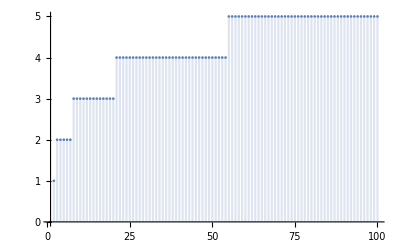

```mathematica
DiscretePlot[Ceiling[Log[x]], {x, 1, 100}]
```

```mathematica
ToString[a]
```

a

```mathematica
FullForm[Out[91]]
```

"a"

```mathematica
String[a,b,c]
```

String[a,b,c]

```mathematica
Head[Out[91]]
```

String

```mathematica
Tail[Out[91]]
```

Tail[a]

```mathematica
StringJoin[a,b,c,d]
```

StringJoin::string: String expected at position 1 in a<>b<>c<>d.

StringJoin::string: String expected at position 2 in a<>b<>c<>d.

StringJoin::string: String expected at position 3 in a<>b<>c<>d.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

a<>b<>c<>d

```mathematica
Map[
ToString,
{a,b,c,d}]
```

{a,b,c,d}

```mathematica
StringJoin[
Map[
ToString,
{a,b,c,d}]]
```

abcd

```mathematica
StringRiffle[StringJoin[
Map[
ToString,
{a,b,c,d}]], "#"]
```

abcd

```mathematica
StringRiffle[
Map[
ToString,
{a,b,c,d}], "#"]
```

a#b#c#d

```mathematica
Characters[
StringRiffle[
Map[
ToString,
{a,b,c,d}], "#"]]
```

{a,#,b,#,c,#,d}

```mathematica
Join[{"#"},Characters[
StringRiffle[
Map[
ToString,
{a,b,c,d}], "#"]],
{"#"}]
```

{#,a,#,b,#,c,#,d,#}

```mathematica
Join[{"#"},Characters[
StringRiffle[
Map[
ToString,
{a,b,c,d}], "#"]],
{"#"}]
```

{#,a,#,b,#,c,#,d,#}

```mathematica
RandomInteger[{0,1}, 10]
```

{1,0,1,1,1,0,0,1,1,1}

```mathematica
With[{list=Out[104]},
Join[{"#"},Characters[
StringRiffle[
Map[
ToString,
list], "#"]],
{"#"}]]
```

{#,1,#,0,#,1,#,1,#,1,#,0,#,0,#,1,#,1,#,1,#}

```mathematica
With[{list=Out[104]},
Join[{"2"},Characters[
StringRiffle[
Map[
ToString,
list], "2"]],
{"#"}]]
```

{2,1,2,0,2,1,2,1,2,1,2,0,2,0,2,1,2,1,2,1,#}

```mathematica
With[{list=Out[104]},
Join[{"#"},Characters[
StringRiffle[
Map[
ToString,
list], "#"]],
{"#"}]]
```

{#,1,#,0,#,1,#,1,#,1,#,0,#,0,#,1,#,1,#,1,#}

```mathematica
Column[{"#","1","#","0","#","1","#","1","#","1","#","0","#","0","#","1","#","1","#","1","#"}]
```

#
1
#
0
#
1
#
1
#
1
#
0
#
0
#
1
#
1
#
1
#

```mathematica
{"#","1","#","0","#","1","#","1","#","1","#","0","#","0","#","1","#","1","#","1","#"}
```

{#,1,#,0,#,1,#,1,#,1,#,0,#,0,#,1,#,1,#,1,#}

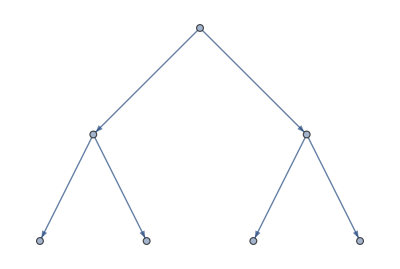

```mathematica
Graph[{1->2,1->3,2->4,2->5,3->6,3->7}]
```

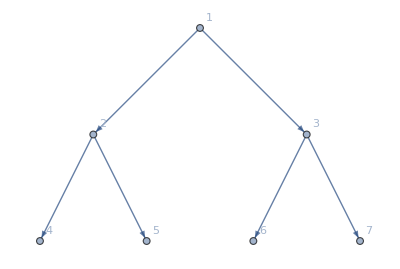

```mathematica
Graph[
Table[Labeled[i, i], {i, 1, 7}],
{1->2,1->3,2->4,2->5,3->6,3->7}]
```

```mathematica
TreeGraph[
Table[Labeled[i, i], {i, 1, 7}],
{1->2,1->3,2->4,2->5,3->6,3->7}]
```

-Graphics-

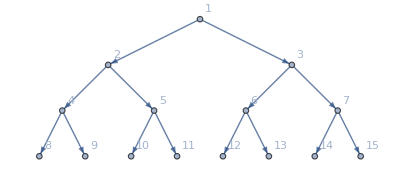

```mathematica
TreeGraph[
Table[Labeled[i, i], {i, 1, 15}],
{1->2,1->3,
2->4,2->5,3->6,3->7,
4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15}]
```

```mathematica
TreeGraph[
Table[Labeled[i, i], {i, 1, 15}],
{1->2,1->3,
2->4,2->5,3->6,3->7,
4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15}]
```

```mathematica
Length@{"#","1","#","0","#","1","#","1","#","1","#","0","#","0","#","1","#","1","#","1","#"}
```

21

```mathematica
TreeGraph[
Table[Labeled[i, i], {i, 1, 15}],
{1->2,1->3,
2->4,2->5,3->6,3->7,
4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15}]
```

```mathematica
{"#","1","#","0","#","1","#","1","#","1","#","0","#","0","#"}
```

{#,1,#,0,#,1,#,1,#,1,#,0,#,0,#}

```mathematica
Length[{"#","1","#","0","#","1","#","1","#","1","#","0","#","0","#"}]
```

15

```mathematica
TreeGraph[
Table[Labeled[i, i], {i, 1, 15}],
{1->2,1->3,
2->4,2->5,3->6,3->7,
4->8,4->9,5->10,5->11,6->12,6->13,7->14,7->15}]
```

-Graphics-

```mathematica
{1,3,1,7,1,7,1,3,1,3,1}
```

{1,3,1,7,1,7,1,3,1,3,1}

```mathematica
Table[
{1, i}->Out[118][[1;;i]],
{i, 1, Length[Out[118]]}]
```

{{1,1}→{1},{1,2}→{1,3},{1,3}→{1,3,1},{1,4}→{1,3,1,7},{1,5}→{1,3,1,7,1},{1,6}→{1,3,1,7,1,7},{1,7}→{1,3,1,7,1,7,1},{1,8}→{1,3,1,7,1,7,1,3},{1,9}→{1,3,1,7,1,7,1,3,1},{1,10}→{1,3,1,7,1,7,1,3,1,3},{1,11}→{1,3,1,7,1,7,1,3,1,3,1}}

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},ColorFunction->"RustTones"]
```

-Graphics3D-

```mathematica
x^2+y^2==-x^2-y^2
```

x^2+y^2==-x^2-y^2

```mathematica
FindInstance[x^2+y^2==-x^2-y^2,{x,y}]
```

{{x→0,y→0}}

```mathematica
Reduce[x^2+y^2==-x^2-y^2]
```

x==-ⅈ y||x==ⅈ y

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},Mesh->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(x^2+y^2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[x y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},
{x,-2,2},{y,-2,2},
BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Grid[Table[Plot3D[Sin[x y],{x,0,4},{y,0,4},PlotPoints->pp,MaxRecursion->mr,Mesh->None],{mr,{0,1,2}},{pp,{5,15}}]]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
{Plot3D[x^4-2 x^2+y^4-2 y^2+5,{x,-2,2},{y,-2,2}],Plot3D[x^4-2 x^2+y^4-2 y^2+1,{x,-2,2},{y,-2,2},PlotRange->{-2,2},ClippingStyle->None]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
{Plot3D[1/(ChebyshevU[x y-1,2]),{x,-5,5},{y,-5,5}],Plot3D[1/(ChebyshevU[x y-1,2]),{x,-5,5},{y,-5,5},Exclusions->{x==0,y==0}]}
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},RegionFunction->Function[{x,y,z},0<x+y^2<Pi]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Sin[x+Cos[x]]
```

Sin[x+Cos[x]]

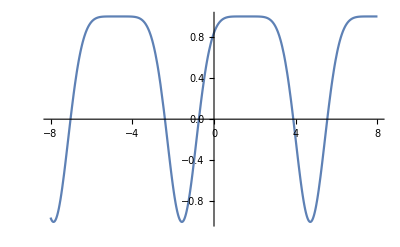

```mathematica
Plot[Sin[x+Cos[x]],{x,-8,8}]
```

```mathematica
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-



```mathematica
Graphics[Disk[{0,0},3]]
```

```mathematica
Graphics[Disk[{0,0},3]]
```

-Graphics-